```mathematica
Sum[Binomial[n,m] p^m(1-p)^(n-m)t^m,{m,0,n}]
```

(1+p (-1+t))^n

```mathematica
g[t_]=Sum[ⅇ^-λ λ^n/n!t^n,{n,0,Infinity}];
g'[1]
g''[1]
```

λ

λ^2

```mathematica
g[t_]=Sum[p q^(n-1)t^n,{n,1,Infinity}];
g'[1]/.q->1-p//Simplify
g''[1]+g'[1]-g'[1]^2/.q->1-p//Simplify
```

1/p

(1-p)/p^2

## Questões 05-07

Crie o hábito de usar Block ao invés de Module. Além disso, para retornar uma função pura, use o Evaluate.

```mathematica
ClearAll[dens,calcChFunc,chFunc]
calcChFunc[ρ_]:=Block[{x,t,charfun,momfun,momt1,momt2},
charfun[t_]=FourierTransform[ρ[x],x,t,FourierParameters->{1,1}];
momt1=Limit[charfun'[t]*(-ⅈ),t->0];
momt2 = Limit[charfun''[t]*(-ⅈ)^2,t->0];
Print["Med: ",momt1];
Print["Var: ",Simplify[momt2-momt1^2]];
Print["Func. característica: ",Simplify@charfun[t]];
momfun[t_]=charfun[-ⅈ t];
Print["Func. momento: ",FullSimplify@ momfun[t]];
Print["Série ψ_X(t): ",Normal@Series[Log[momfun[t]],{t,0,4}]];
Evaluate[charfun[#]]&
];
```

Distribuição uniforme

```mathematica
dens[x_]:=Piecewise[{{1/(b-a),a<=x<=b}}];
chFunc=calcChFunc[dens[#]&];
```

Med: Piecewise[{{(a+b)/2, a<b}, {0, True}}]

Var: Piecewise[{{1/12 (a-b)^2, a<b}, {0, True}}]

Func. característica: (ⅈ (ⅇ^(ⅈ a t)-ⅇ^(ⅈ b t)) (-1+UnitStep[a-b]))/((a-b) t)

Func. momento: -((ⅇ^(a t)-ⅇ^(b t)) (-1+UnitStep[a-b]))/((a-b) t)

Série ψ_X(t): 1/2 (a+b) t+1/24 (a^2-2 a b+b^2) t^2+((-a^4+4 a^3 b-6 a^2 b^2+4 a b^3-b^4) t^4)/2880+Log[1-UnitStep[a-b]]

Distribuição exponencial

```mathematica
dens[x_]:=Piecewise[{{λ ⅇ^(-λ x),x>=0}}];
chFunc=calcChFunc[dens[#]&];
```

Med: 1/λ

Var: 1/λ^2

Func. característica: (ⅈ λ)/(t+ⅈ λ)

Func. momento: -λ/(t-λ)

Série ψ_X(t): t^4/(4 λ^4)+t^3/(3 λ^3)+t^2/(2 λ^2)+t/λ

Distribuição gama:

```mathematica
dens[x_]:=Piecewise[{{λ^p ⅇ^(-λ x)x^(p-1)/Gamma[p],x>=0}}];
chFunc=calcChFunc[dens[#]&];
```

Med: p/λ

Var: p/λ^2

Func. característica: (1+t^2/λ^2)^(-p/2) (Cos[p ArcTan[t/λ]]+ⅈ Sin[p ArcTan[t/λ]])

Func. momento: (1-t^2/λ^2)^(-p/2) (Cosh[p ArcTanh[t/λ]]+Sinh[p ArcTanh[t/λ]])

Série ψ_X(t): (p t^4)/(4 λ^4)+(p t^3)/(3 λ^3)+(p t^2)/(2 λ^2)+(p t)/λ

## Questão 11:

```mathematica
pdfV[v_]=PDF[NormalDistribution[0,s],v];
funcI[v_]=i0*(ⅇ^((e v)/(k T))-1);
Solve[funcI[v]==i,v,Reals];
vroot = k T/e Log[(i+i0)/i0];
1/funcI'[vroot]//Simplify
pdfI[i_]=(k T)/(e(i+i0))*pdfV[vroot]//Simplify
```

(k T)/(e (i+i0))

(ⅇ^(-(k^2 T^2 Log[(i+i0)/i0]^2)/(2 e^2 s^2)) k T)/(√(2 π) (e i s+e i0 s))

Como aprendido em MCA, o Mathematica tem problemas para avaliar integrais definidas ocasionalmente. Para resolver o problema, ou avalie a integral indefinida e faça a subtração nos limites com os critérios de simplificação ou avalie a integral diretamente com os domínios de cada parâmetro simbólico.

Can't compute definite integral, but can compute indefinite

Método 1: integrando na PDF da corrente, indefinidas

```mathematica
int[i_]=Integrate[i pdfI[i],i];
Simplify[int[∞]-int[-i0],{k>0,T>0,e>0,s>0}]
```

(-1+ⅇ^((e^2 s^2)/(2 k^2 T^2))) i0

Método 2: integrando na PDF da tensão, definida com simplificações

```mathematica
Integrate[funcI[v]*pdfV[v],{v,-Infinity,Infinity},Assumptions->{s>0,e>0,T>0,k>0}]
```

(-1+ⅇ^((e^2 s^2)/(2 k^2 T^2))) i0

Método 3: integrando na PDF da corrente, integral definida com domínios explícitos

```mathematica
Integrate[i pdfI[i],{i,-i0,Infinity},Assumptions->{s>0,e>0,T>0,k>0}]//Simplify
```

(-1+ⅇ^((e^2 s^2)/(2 k^2 T^2))) i0

Plotando por transofmração direta da PDF:

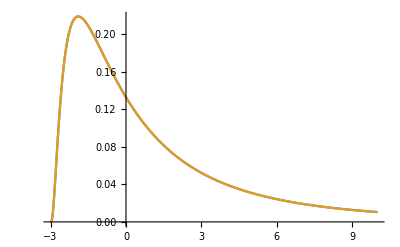

```mathematica
transformedPdfI[i_]=PDF[TransformedDistribution[3*(Exp[v]-1),v\[Distributed]NormalDistribution[0,1]],i];
Plot[
{transformedPdfI[i]/.{s->1,k->1,T->1,e->1,i0->3}//N,
pdfI[i]/.{s->1,k->1,T->1,e->1,i0->3}},
{i,-3,10},PlotRange->Full]
```

Encontrando o máximo e o valor mais provável da PDF:

```mathematica
sol=Solve[D[pdfI[i],i]==0,i];sol[[1,1]]//Simplify
pdfI[i]/.sol[[1]]//FullSimplify[#,Assumptions->{s>0,e>0,T>0,k>0}]&
```

i→(-1+ⅇ^(-(e^2 s^2)/(k^2 T^2))) i0

(ⅇ^((e^2 s^2)/(2 k^2 T^2)) k T)/(e i0 √(2 π) s)

## Questão 12

```mathematica
Zvec={√(-2Log[U1])Cos[2π U2],√(-2Log[U1])Sin[2π U2]};
Uvec={U1,U2};
invJac=D[Zvec,{Uvec}];
invJacDet=Det[D[Zvec,{Uvec}]]//Simplify;
jac=1/invJacDet
```

-U1/(2 π)

```mathematica
Solve[{Z1==Zvec[[1]],Z2==Zvec[[2]]},{U1,U2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{U1→ⅇ^(1/2 (-Z1^2-Z2^2)),U2→-ArcCos[(ⅈ Z1 √(-Z1^2-Z2^2))/(Z1^2+Z2^2)]/(2 π)},{U1→ⅇ^(1/2 (-Z1^2-Z2^2)),U2→ArcCos[(ⅈ Z1 √(-Z1^2-Z2^2))/(Z1^2+Z2^2)]/(2 π)}}

## Questão 13

```mathematica
ClearAll[a,n,sol]
sol=RSolve[{a[n]==(1-p)(a[n-1]+p*a[n-2]),
a[1]==1-p,a[2]==(1-p)^2+p(1-p)},a[n],n];
a[n_,p_]=a[n]/.sol[[1]];
c[n_,p_]=a[n-1,p]+(1-p)*p*a[n-2,p];
c[10,0.3]//Simplify
(*Totalmente coerente com a lista 1A caso p=0.5*)
```

0.496412

## Questão 14

```mathematica
ClearAll[sol,a,n,p]
sol = RSolve[{a[n]==p+a[n-1]*(1-2p),a[1]==1-p},a[n],n];
a[n_,p_]=a[n]/.sol[[1]];
a[7,69/77]//N
```

0.402086